# Notebook: NLS stability problem

```mathematica
Clear["`*"]
(* This solves the Hamiltonian eigenvalue problem L+ u = λ v    L- v = - λ u 
where L+- are second order periodic differential operators. It computes the spectrum using a spectral method as well as 
computing the Floquet discriminant along the imaginary axis. *)

a0 = -4;
a1 = 3;
a2 = 2;
b0 = -6;
b1 = -1;
b2 = 3; 
(* The a and b coefficients are the coefficients of the constant cos(x) and sin(2x) terms respectively. 
the matrices md2, md1 and md0 represent the second derivative, first derivative and identity matrix respectively *)
```

```mathematica
(* Define the bifurcation index in terms of the resultant of the characteristic polynomial and its derivative with respect to the spectral parameter f and g are the two invariants and fp and gp are their derivatives. *)
(* This is actually the square root of the bifurction index.*)
```

```mathematica
Bifurcation[f_?NumericQ,g_?NumericQ,fp_?NumericQ,gp_?NumericQ] := -2 fp^2+fp^2 g-f fp gp+gp^2;
```

```mathematica
(* Set up the matrices for solving the eigenvalue problem using a spectral method *)
```

```mathematica
nmodes = 15; 
md2 = DiagonalMatrix[Table[1.0 i^2,{i,-
nmodes,nmodes}]];
md1 = DiagonalMatrix[Table[1.0 i,{i,-
nmodes,nmodes}]];
md0=IdentityMatrix[2 nmodes+1];
```

```mathematica
qpm = a0 md0+a1*Normal[SparseArray[{Band[{1,2}]->.5,Band[{2,1}]->.5},{2nmodes+1,2nmodes+1}]]+
a2*Normal[SparseArray[{Band[{1,3}]->.5I,Band[{3,1}]->-.5I},{2nmodes+1,2nmodes+1}]];
qmm = b0 md0+b1*Normal[SparseArray[{Band[{1,2}]->.5,Band[{2,1}]->.5},{2nmodes+1,2nmodes+1}]]+
b2*Normal[SparseArray[{Band[{1,3}]->.5I,Band[{3,1}]->-.5I},{2nmodes+1,2nmodes+1}]];

(* Generate the derivative matrices and the potentials *)
```

```mathematica
om = DiagonalMatrix[Table[0,{i,-nmodes,nmodes}]];
```

```mathematica
bm[μ_]:=ArrayFlatten[{{om,md2-2μ md1+μ^2 md0+qpm},{-(md2-2μ md1 + μ^2 md0 + qmm),om}}]
```

```mathematica
evals=Flatten[Table[Eigenvalues[bm[μ]],{μ,-1,1,0.003}]];
```

```mathematica
bvals[μ_]:=I*Eigenvalues[bm[μ]]
```

```mathematica
sm[μ_]:=ComplexListPlot[bvals[μ],PlotRange->{{-4,4},{-4,4}},PlotStyle->{Thick,Blue,PointSize[0.01]}]
```

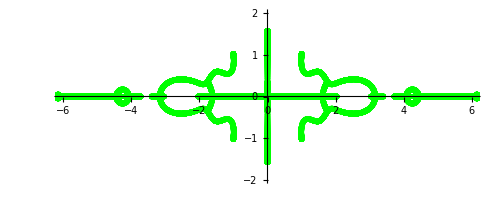

```mathematica
s1=ComplexListPlot[I*evals,PlotRange->{{-6,6},{-2,2}},PlotStyle->{Thick,Green,PointSize[0.01]}]
```

```mathematica
(* The manipulate below lets us play around with the spectrum  but it is very slow*)
```

```mathematica
(* Manipulate[Show[{s1,sm[μ]},ImageSize->Medium],{μ,0,1,0.01}] *)
```

```mathematica
qqp[x_]:= a0+a1 Cos[x]+a2 Sin[2x]
qqm[x_]:= b0 + b1 Cos[x]+b2 Sin[2x]
```

```mathematica
(* These are the potentials in the problem*)
```

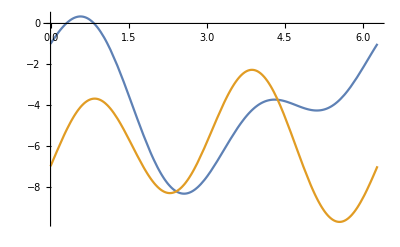

```mathematica
Plot[{qqp[x],qqm[x]},{x,0,2*Pi}]
```

```mathematica
(* The matrices generating the two symmetries.*)
```

```mathematica
bb = {{0,0,1,0},{0,0,0,-1},{qqp[x],-λ,0,0},{-λ,-qqm[x],0,0}}
```

{{0,0,1,0},{0,0,0,-1},{-4+3 Cos[x]+2 Sin[2 x],-λ,0,0},{-λ,6+Cos[x]-3 Sin[2 x],0,0}}

```mathematica
jj ={{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}}
```

{{0,0,1,0},{0,0,0,1},{-1,0,0,0},{0,-1,0,0}}

```mathematica
vv=-{{0,0,-1,0},{0,0,0,1},{1,0,0,0},{0,-1,0,0}}
```

{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}}

```mathematica
(*WorkingPrecision->20,AccuracyGoal->20*)
```

```mathematica
(* The code block below solves the differential equation for four different starting conditions and generates the monodromy matrix. It alos generates the equation of variation/tangent flow to compute derivatives. *)
```

```mathematica
sol1 = ParametricNDSolveValue[{u'[x1]==p[x1],w'[x1]==r[x1],v'[x1]==-q[x1],y'[x1]==-s[x1],p'[x1]==qqp[x1]u[x1]-λ*v[x1],r'[x1]==qqp[x1]w[x1]-λ*y[x1]-v[x1],q'[x1]==-λ*u[x1]-qqm[x1]v[x1],s'[x1]==-λ*w[x1]-qqm[x1]y[x1]- u[x1],u[0]==1,v[0]==0,p[0]==0,q[0]==0,w[0]==0,y[0]==0, r[0]==0,s[0]==0},{u,v,p,q,w,y,r,s},{x1,0,25},{λ}];
sol2 = ParametricNDSolveValue[{u'[x1]==p[x1],w'[x1]==r[x1],v'[x1]==-q[x1],y'[x1]==-s[x1],p'[x1]==qqp[x1]u[x1]-λ*v[x1],r'[x1]==qqp[x1]w[x1]-λ*y[x1]-v[x1],q'[x1]==-λ*u[x1]-qqm[x1]v[x1],s'[x1]==-λ*w[x1]-qqm[x1]y[x1]- u[x1],u[0]==0,v[0]==1,p[0]==0,q[0]==0,w[0]==0,y[0]==0, r[0]==0,s[0]==0},{u,v,p,q,w,y,r,s},{x1,0,25},{λ}];
sol3 = ParametricNDSolveValue[{u'[x1]==p[x1],w'[x1]==r[x1],v'[x1]==-q[x1],y'[x1]==-s[x1],p'[x1]==qqp[x1]u[x1]-λ*v[x1],r'[x1]==qqp[x1]w[x1]-λ*y[x1]-v[x1],q'[x1]==-λ*u[x1]-qqm[x1]v[x1],s'[x1]==-λ*w[x1]-qqm[x1]y[x1]- u[x1],u[0]==0,v[0]==0,p[0]==1,q[0]==0,w[0]==0,y[0]==0, r[0]==0,s[0]==0},{u,v,p,q,w,y,r,s},{x1,0,25},{λ}];
sol4 = ParametricNDSolveValue[{u'[x1]==p[x1],w'[x1]==r[x1],v'[x1]==-q[x1],y'[x1]==-s[x1],p'[x1]==qqp[x1]u[x1]-λ*v[x1],r'[x1]==qqp[x1]w[x1]-λ*y[x1]-v[x1],q'[x1]==-λ*u[x1]-qqm[x1]v[x1],s'[x1]==-λ*w[x1]-qqm[x1]y[x1]- u[x1],u[0]==0,v[0]==0,p[0]==0,q[0]==1,w[0]==0,y[0]==0, r[0]==0,s[0]==0},{u,v,p,q,w,y,r,s},{x1,0,25},{λ}];
```

```mathematica
per=2Pi;
```

```mathematica
mm[λ_]:={{sol1[λ][[1]][per],sol2[λ][[1]][per],sol3[λ][[1]][per],sol4[λ][[1]][per]},{sol1[λ][[2]][per],sol2[λ][[2]][per],sol3[λ][[2]][per],sol4[λ][[2]][per]},{sol1[λ][[3]][per],sol2[λ][[3]][per],sol3[λ][[3]][per],sol4[λ][[3]][per]},{sol1[λ][[4]][per],sol2[λ][[4]][per],sol3[λ][[4]][per],sol4[λ][[4]][per]}};
mmp[λ_]:={{sol1[λ][[5]][per],sol2[λ][[5]][per],sol3[λ][[5]][per],sol4[λ][[5]][per]},{sol1[λ][[6]][per],sol2[λ][[6]][per],sol3[λ][[6]][per],sol4[λ][[6]][per]},{sol1[λ][[7]][per],sol2[λ][[7]][per],sol3[λ][[7]][per],sol4[λ][[7]][per]},{sol1[λ][[8]][per],sol2[λ][[8]][per],sol3[λ][[8]][per],sol4[λ][[8]][per]}}
```

```mathematica
f[λ_?NumericQ]:= Tr[mm[λ]]
g[λ_?NumericQ]:= (Tr[mm[λ]]^2-Tr[mm[λ].mm[λ]])/2
fp[λ_?NumericQ] := Tr[mmp[λ]]
gp[λ_?NumericQ] := Tr[mm[λ]] Tr[mmp[λ]] - Tr[mm[λ].mmp[λ]]
CP = x^4 - f[λ] x^3 + g[λ] x^2 - f[λ] x + 1;
ωp[λ_?NumericQ]:= 1/2(f[λ]+Sqrt[f[λ]^2-4*(g[λ]-2)])
ωm[λ_?NumericQ]:= 1/2(f[λ]-Sqrt[f[λ]^2-4*(g[λ]-2)])
CP = x^4 - f[λ] x^3 + g[λ] x^2 - f[λ] x + 1 ;
CPS = (2+2 f[λ]+g[λ]) τ^4 + (12+2 g[λ])τ^2  + (2-2 f[λ]+g[λ])
A0 =(2+2 f[λ]+g[λ]) 
C0 = ( 12+2 g[λ])
E0 = (2-2 f[λ]+g[λ])
Disco[λ_] := 256-192 f[λ]^2-60 f[λ]^4-4 f[λ]^6+288 f[λ]^2 g[λ]+36 f[λ]^4 g[λ]-128 g[λ]^2-80 f[λ]^2 g[λ]^2+f[λ]^4 g[λ]^2-8 f[λ]^2 g[λ]^3+16 g[λ]^4
P[λ_] := 8(2+2 f[λ]+g[λ]) ( -12+2 g[λ]) 
D0[λ_]:= 64 (2+2 f[λ]+g[λ]) ^3 (2-2 f[λ]+g[λ]) - 16 (2+2 f[λ]+g[λ])^2 (- 12+2 g[λ])^2
Multi[λ_] := If[Re[Disco[λ]]<0,2,If[Re[P[λ]]<0 && Re[D0[λ]]<0,4,0]]
Bifurcation2[λ_]:=Bifurcation[f[λ],g[λ],fp[λ],gp[λ]]
Discriminant[CP,x]
```

2-2 f[λ]+g[λ]+τ^4 (2+2 f[λ]+g[λ])+τ^2 (12+2 g[λ])

2+2 f[λ]+g[λ]

12+2 g[λ]

2-2 f[λ]+g[λ]

256-192 f[λ]^2-60 f[λ]^4-4 f[λ]^6+288 f[λ]^2 g[λ]+36 f[λ]^4 g[λ]-128 g[λ]^2-80 f[λ]^2 g[λ]^2+f[λ]^4 g[λ]^2-8 f[λ]^2 g[λ]^3+16 g[λ]^4

```mathematica
Factor[Discriminant[CP,x]]
```

-(8+f[λ]^2-4 g[λ])^2 (-2+2 f[λ]-g[λ]) (2+2 f[λ]+g[λ])

```mathematica
mm[1.0I]//MatrixForm
```

(-0.678373+0. ⅈ | 0.-1.39847 ⅈ | -0.876865+0. ⅈ | 0.-0.393123 ⅈ
0.-0.0127327 ⅈ | -0.50428+0. ⅈ | 0.-0.517632 ⅈ | 0.101353+0. ⅈ
0.0540242+0. ⅈ | 0.-1.48016 ⅈ | 0.172121+0. ⅈ | 0.+0.348598 ⅈ
0.-2.12217 ⅈ | 0.74493+0. ⅈ | 0.-2.28644 ⅈ | -0.0121164+0. ⅈ)

```mathematica
CharacteristicPolynomial[mm[1.0I],μ]
```

(0.999999-1.27676×10^-15 ⅈ)+(1.02265-1.33227×10^-15 ⅈ) μ+(0.943855-2.22045×10^-16 ⅈ) μ^2+(1.02265+4.44089×10^-16 ⅈ) μ^3+μ^4

```mathematica
(* Symmetry checks out up to some small numerical error *)
```

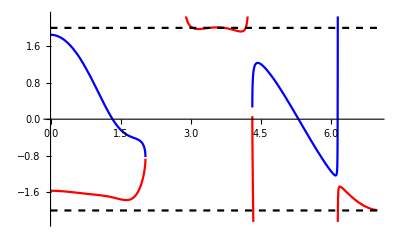

```mathematica
s2=Plot[{ωp[I*β],ωm[I*β],2,-2},{β,0,7},PlotStyle->{Blue,Red,{Black,Dashed},{Black,Dashed}},PlotRange->{-2.25,2.25}]
```

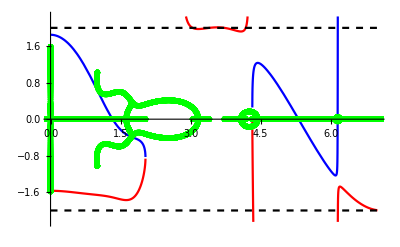

```mathematica
Show[{s2,s1}]
```

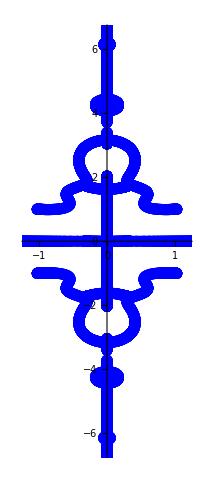

```mathematica
SpecPlot=ComplexListPlot[evals,PlotRange->{{-1.2,1.2},{-6.5,6.5}},PlotStyle->{Thick,Blue,PointSize[0.02]}]
```

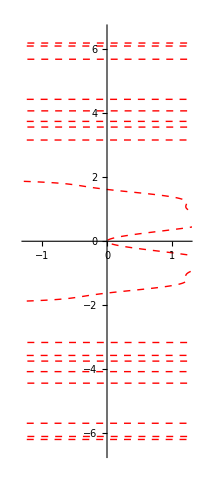

```mathematica
BifPlot=ParametricPlot[{Re[Bifurcation2[I x]],x},{x,-6.5,6.5},PlotStyle->{Thick,Red,Dashed},PlotRange->{{-1.25,1.25},{-6.5,6.5}}]
```

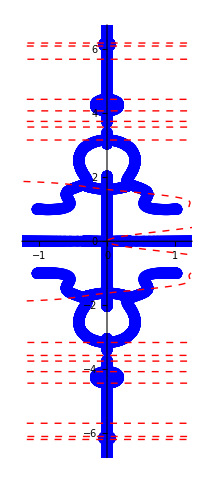

```mathematica
Show[SpecPlot,BifPlot]
```

```mathematica
Multi[λ_] := If[Re[Disco[λ]]<0,2I,If[Re[P[λ]]<0 && Re[D0[λ]]<0,4,I]]
```

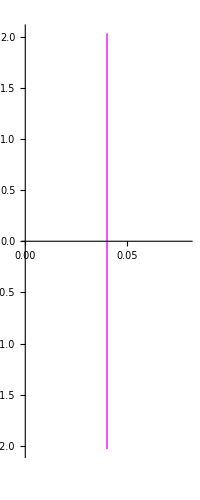

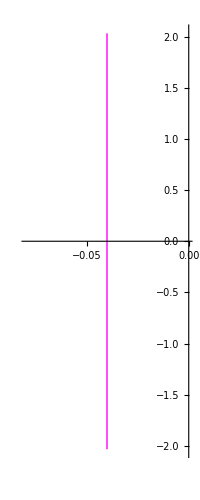

```mathematica
s1a = ParametricPlot[{.01 Multi[I x],x},{x,-6.5,6.5},PlotStyle->{Magenta,Thick}]
s1b = ParametricPlot[{-.01 Multi[I x],x},{x,-6.5,6.5},PlotStyle->{Magenta,Thick}]
```

```mathematica
Figure11b=Show[s2,s1]
```

-Graphics-

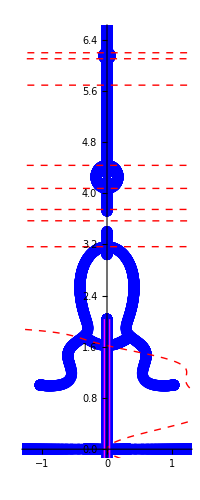

```mathematica
PaperFigure = Show[SpecPlot,BifPlot, s1a,s1b,PlotRange->{{-1.25,1.25},{0,6.5}}]
```

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/NLS/Figure11a.pdf",PaperFigure]
```

~/Dropbox/Jared Robby/Schmoopys/NLS/Figure11a.pdf

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/NLS/Figure11a.png",PaperFigure]
```

~/Dropbox/Jared Robby/Schmoopys/NLS/Figure11a.png

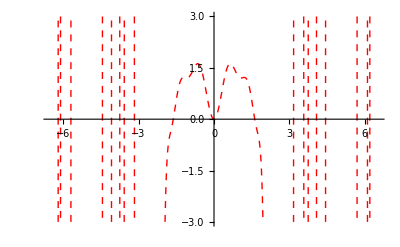

```mathematica
BifPlot2=Plot[Re[Bifurcation2[I x]],{x,-6.5,6.5},PlotStyle->{Thick,Red,Dashed},PlotRange->{{-6.5,6.5},{-3,3}}]
```

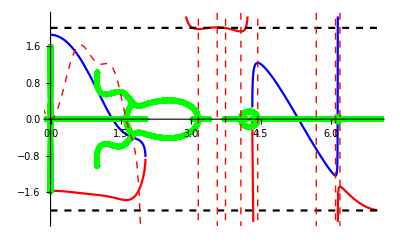

```mathematica
Figure2=Show[s2,s1,BifPlot2]
```